## You can (sometimes) hear the shape of isospectral drums by choosing where to drum them.

Emilio Pisanty, 2016.

This notebook provides a partial answer to a question I posed on MathOverflow, Can one hear the shape of a drum by choosing where to drum it?, in the positive. In particular, I provide an example of two isospectral surfaces (in fact, one of the canonical examples of such pairs) which nevertheless produce different timbres when drummed appropriately.

Begin by setting up the regions D_1 and D_2 as in Gordon and Webb’s American Scientist 84 no. 1, 46 (1996). It is a nice exercise to show that these two surfaces are isospectral, which can be done by snipping D_1 into triangles and then taking linear combinations of the D_1 eigenfunctions on a triangle mesh on D_2.

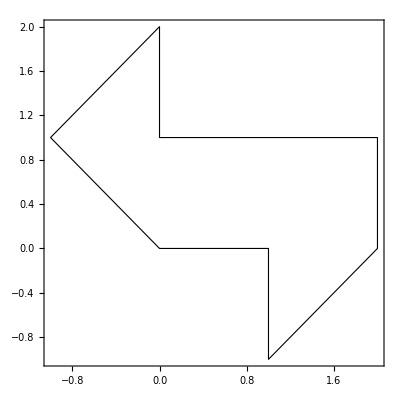
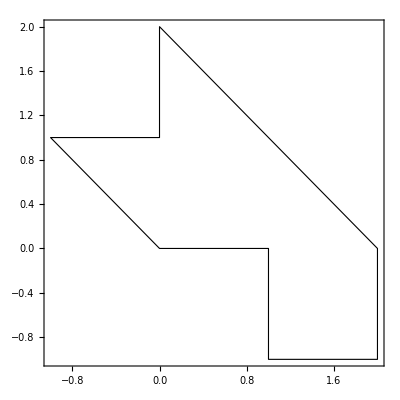

```mathematica
Row[{
Show[{
Dgraphic[1]=Graphics[{EdgeForm[{Thick,Black}],Opacity[0],
region[1]=Polygon[{{0,0},{1,0},{1,-1},{2,0},{2,1},{0,1},{0,2},{-1,1}}]
}]
},Frame->True,ImageSize->400],
Show[{
Dgraphic[2]=Graphics[{EdgeForm[{Thick,Black}],Opacity[0],
region[2]=Polygon[{{0,0},{1,0},{1,-1},{2,-1},{2,0},{0,2},{0,1},{-1,1}}]
}]
},Frame->True,ImageSize->400]
}]
```

To evaluate the timbres of the sounds produced by the two drums, we want to numerically solve the Helmholtz equation on the two domains, so we can have access to the eigenfunctions. To do this I will use the code posted by user21 and packaged up by Mark McClure in response to this question on mathematica.stackexchange ppp, given below.

```mathematica
Needs["NDSolve`FEM`"];
helmholzSolve[g_,numEigenToCompute_Integer,opts:OptionsPattern[]]:=Module[
{u,x,y,t,pde,dirichletCondition,mesh,boundaryMesh,nr,state,femdata,initBCs,methodData,initCoeffs,vd,sd,discretePDE,discreteBCs,load,stiffness,damping,pos,nDiri,numEigen,res,eigenValues,eigenVectors,evIF},

(*Discretize the region*)
If[
Head[g]===ImplicitRegion||Head[g]===ParametricRegion
,mesh=ToElementMesh[DiscretizeRegion[g],opts]
,mesh=ToElementMesh[DiscretizeGraphics[g],opts]
];
boundaryMesh=ToBoundaryMesh[mesh];

(*Set up the PDE and boundary condition*)
pde=D[u[t,x,y],t]-Laplacian[u[t,x,y],{x,y}]+u[t,x,y]==0;
dirichletCondition=DirichletCondition[u[t,x,y]==0,True];

(*Pre-process the equations to obtain the FiniteElementData in StateData*)
nr=ToNumericalRegion[mesh];
{state}=NDSolve`ProcessEquations[{pde,dirichletCondition,u[0,x,y]==0},u,{t,0,1},Element[{x,y},nr]];
femdata=state["FiniteElementData"];
initBCs=femdata["BoundaryConditionData"];
methodData=femdata["FEMMethodData"];
initCoeffs=femdata["PDECoefficientData"];

(*Set up the solution*)
vd=methodData["VariableData"];
sd=NDSolve`SolutionData[{"Space"->nr,"Time"->0.}];

(*Discretize the PDE and boundary conditions*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
discreteBCs=DiscretizeBoundaryConditions[initBCs,methodData,sd];

(*Extract the relevant matrices and deploy the boundary conditions*)
load=discretePDE["LoadVector"];
stiffness=discretePDE["StiffnessMatrix"];
damping=discretePDE["DampingMatrix"];
DeployBoundaryConditions[{load,stiffness,damping},discreteBCs];

(*Set the number of eigenvalues ignoring the Dirichlet positions*)
pos=discreteBCs["DirichletMatrix"]["NonzeroPositions"][[All,2]];
nDiri=Length[pos];
numEigen=numEigenToCompute+nDiri;

(*Solve the eigensystem*)
res=Eigensystem[{stiffness,damping},-numEigen];
res=Reverse/@res;
eigenValues=res[[1,nDiri+1;;Abs[numEigen]]];
eigenVectors=res[[2,nDiri+1;;Abs[numEigen]]];
evIF=ElementMeshInterpolation[{mesh},#]&/@eigenVectors;

(*Return the relevant information*)
{eigenValues,evIF,mesh}
]
```

The solver is relatively fast:

```mathematica
AbsoluteTiming[
Table[
{ev[i],if[i],mesh[i]}=helmholzSolve[Graphics[region[i]],10]
,{i,1,2}]
]
```

{3.36072,{{{11.1886,15.6614,21.7808,27.1897,30.0825,37.9283,43.5101,47.3032,50.4921,53.4794},{InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>]},ElementMesh[{{-1.,2.},{-1.,2.}},{TriangleElement[<250>]}]},{{11.1843,15.6581,21.7738,27.197,30.0764,37.9251,43.5215,47.3124,50.508,53.5312},{InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>],InterpolatingFunction[{{-1., 2.}, {-1., 2.}}, <>]},ElementMesh[{{-1.,2.},{-1.,2.}},{TriangleElement[<235>]}]}}}

To evaluate the accuracy of the solver, we can begin by looking at how isospectral it thinks the surfaces are:

```mathematica
ev[1]/ev[2]
Abs[ev[1]/ev[2]-1]
Abs[ev[1]/ev[2]-1]//Sort
```

{1.00039,1.00021,1.00032,0.999732,1.0002,1.00008,0.999738,0.999806,0.999687,0.999033}

{0.000389232,0.000211747,0.000320606,0.000268003,0.000202663,0.0000841948,0.000262202,0.000193833,0.000312998,0.000967204}

{0.0000841948,0.000193833,0.000202663,0.000211747,0.000262202,0.000268003,0.000312998,0.000320606,0.000389232,0.000967204}

So the eigenvalues agree to a few parts in 10^-4, which looks pretty reasonable as a first start. For the qualitative points that I will make later on, this feels like more than enough.

So, now that we have the eigenfunctions, let’s have a quick look at the first few of them.

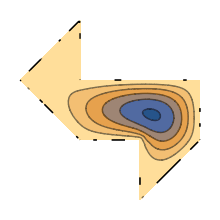
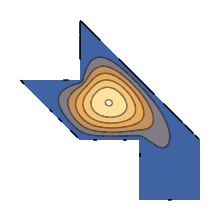
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Quiet@Table[
Show[{
ContourPlot[
if[i]⟦k⟧[x,y]
,{x,y}∈region[i]
,PlotRange->All
,PlotPoints->150
,ImageSize->220
],
ContourPlot[
if[i]⟦k⟧[x,y]==0
,{x,y}∈region[i]
,PlotPoints->100
,ContourStyle->{{Thick,Black}}
],
Dgraphic[i]
}
,Frame->None
]
,{i,1,2},{k,1,4}]
Export[FileNameJoin[{NotebookDirectory[],"eigenfunction overview.png"}],Show[GraphicsGrid[%],ImageSize->800]];
```

The thick black lines are the zero contours of the eigenfunctions, i.e. the nodes of the normal modes of the two drums.

The zeros are the crucial part of the story. In particular, consider the nodes for the second and fourth eigenfunctions, shown in black and red below:

```mathematica
Table[
Show[{
Quiet@ContourPlot[
{if[i]⟦2⟧[x,y]==0,if[i]⟦4⟧[x,y]==0}
,{x,y}∈region[i]
,PlotPoints->200
,ContourStyle->{{Thick,Black},{Thick,Darker[Red,0.2]}}
,ImageSize->350
],
Dgraphic[i]
}
,Frame->None
]
,{i,1,2}]
Export[FileNameJoin[{NotebookDirectory[],"eigenfunction 2, 4 nodes.png"}],Show[GraphicsRow[%],ImageSize->800]];
```

{-Graphics-,-Graphics-}

The crucial point is that the node of φ_2 on D_2 intersects a node of φ_4, but on D_1 there is no such intersection. This means that on D_2 a smart drummer can hit the drum at this intersection, and this will produce a sound with significant components of λ_1, λ_3, λ_5, λ_6, λ_7, and so on, but with zero Fourier coefficient at frequency λ_2 and λ_4. Conversely, a drummer hitting D_1 can produce timbres with no λ_2 component or with no λ_4 component, but they can never eliminate both components simultaneously. Thus the D_2 drummer can show unambiguously that they are not using D_1.

The opposite happens when one compares the nodes of φ_2 with φ_5:

```mathematica
Table[
Show[{
Quiet@ContourPlot[
{if[i]⟦2⟧[x,y]==0,if[i]⟦5⟧[x,y]==0}
,{x,y}∈region[i]
,PlotPoints->200
,ContourStyle->{{Thick,Black},{Thick,Darker[Red,0.2]}}
,ImageSize->350
],
Dgraphic[i]
}
,Frame->None
]
,{i,1,2}]
Export[FileNameJoin[{NotebookDirectory[],"eigenfunction 2, 5 nodes.png"}],Show[GraphicsRow[%],ImageSize->800]];
```

{-Graphics-,-Graphics-}

Here the nodes intersect on D_1 but not on D_2, so a clever drummer can show conclusively that they are not using D_2.

That’s about it, really: isospectral surfaces can be acoustically distinguishable.